```mathematica
HorbBase = Vt/2 σX-((e*ΔE*d)/(2h))σZ;
{β, α} = Eigensystem[HorbBase][[2]][[2]] // Normalize // FullSimplify;
α = -α;

iState = {α, β};
dState = {β, -α};
ii = Outer[Times, iState, iState] // FullSimplify;
id = Outer[Times, iState, dState] // FullSimplify;
di = Outer[Times, dState, iState] // FullSimplify;
dd = Outer[Times, dState, dState] // FullSimplify;

M = {{α, β}, {β, -α}};
Transpose[M].HorbBase.M // FullSimplify // MatrixForm

(ii - dd) // FullSimplify // MatrixForm

-((e*(ΔE + Eac*Cos[2*π*νE*t])*d)/(2h))*(ii - dd) + (Vt/2)(id + di) // FullSimplify // MatrixForm
```

(-(√(h^2 Vt^2+d^2 e^2 ΔE^2))/(2 h) | 0
0 | (√(h^2 Vt^2+d^2 e^2 ΔE^2))/(2 h))

((d e ΔE)/(√(h^2 Vt^2+d^2 e^2 ΔE^2)) | -(h Vt)/(√(h^2 Vt^2+d^2 e^2 ΔE^2))
-(h Vt)/(√(h^2 Vt^2+d^2 e^2 ΔE^2)) | -(d e ΔE)/(√(h^2 Vt^2+d^2 e^2 ΔE^2)))

(-(h^2 Vt^2+d^2 e^2 ΔE^2+d^2 e^2 Eac ΔE Cos[2 π t νE])/(2 h √(h^2 Vt^2+d^2 e^2 ΔE^2)) | (d e Eac Vt Cos[2 π t νE])/(2 √(h^2 Vt^2+d^2 e^2 ΔE^2))
(d e Eac Vt Cos[2 π t νE])/(2 √(h^2 Vt^2+d^2 e^2 ΔE^2)) | (h^2 Vt^2+d^2 e^2 ΔE^2+d^2 e^2 Eac ΔE Cos[2 π t νE])/(2 h √(h^2 Vt^2+d^2 e^2 ΔE^2)))

{5.65426×10^9,-5.62524×10^9,-5.62501×10^9,5.59599×10^9,-4.65445×10^7,3.0935×10^7,1.72977×10^7,-1.68496×10^6}

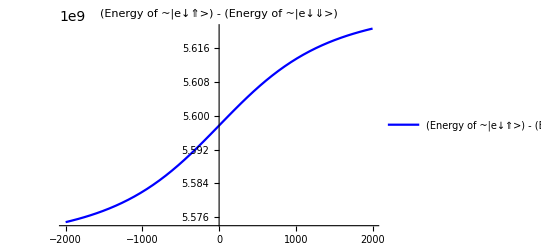

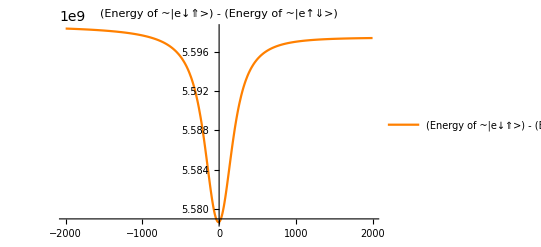

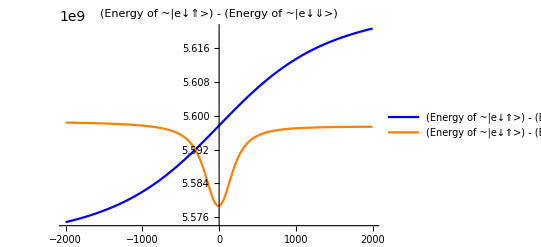

```mathematica
HB0=-B0 (γe*TProduct[(σI+Δγ*dd),Sz, σI]-γn*TProduct[σI,σI, Iz]);
HA=TProduct[A*dd,SdotI];
Horb=TProduct[-((e*(ΔE + Eac*Cos[2*π*νE*t])*d)/(2h))*(ii - dd) + (Vt/2)(id + di), σI, σI];
HESR = Bac*Sin[2*π*νB*t](γe*TProduct[σI,Sx, σI]-γn*TProduct[σI,σI, Ix]);

HnsInGE = δB*TProduct[σI, Sz, σI] - (γn*B0 + νB)*TProduct[σI, σI, Iz] + (Bac/2)(γe*TProduct[σI, Sx, σI] - γn*TProduct[σI, σI, Ix]) + Horb + HA;

H = HB0 + HESR + HA + Horb;

HtoPlot = HnsInGE;

setVariables[];

B0 = B0;
(* set Bac *)
Bac = .000;
Vt = Vt*1;
νB = νB*1;

energiesAt[Ef_] := Eigensystem[HtoPlot /. {ΔE -> Ef}][[1]]
statesAt[Ef_] := Eigensystem[HtoPlot /. {ΔE -> Ef}][[2]]
systemAt[Ef_] := Eigensystem[HtoPlot /. {ΔE -> Ef}]
energiesAtZero = energiesAt[0];

targetStates = IdentityMatrix[8];
order[Ef_] := Table[Ordering[row, -1][[1]], {row,Abs[targetStates.ConjugateTranspose[statesAt[Ef]]]}]

statesAtZero = statesAt[0];

makePlot[iA_, iB_, color_] := Plot[
{
energiesAt[Ef][[order[Ef][[iA]]]] - energiesAt[Ef][[order[Ef][[iB]]]]
},
 {Ef, -2000, 2000},
PlotLabel->"(Energy of ~"<>ToString[basisGE[[iA]]]<>") - (Energy of ~"<>ToString[basisGE[[iB]]]<>")",
PlotLegends->{"(Energy of ~"<>ToString[basisGE[[iA]]]<>") - (Energy of ~"<>ToString[basisGE[[iB]]]<>")"},
PlotRange->All,
PlotStyle-> color
]

energiesAt[0]

pNSpin = makePlot[6, 5, Blue]

pFF = makePlot[6, 7, Orange]

Show[pNSpin, pFF, PlotRange-> All]

clearVariables[];
```